D:\Documents\Research\C-C++Code\FuzzyPriorwEpochs\FuzzyPriorwEpochs\Debug

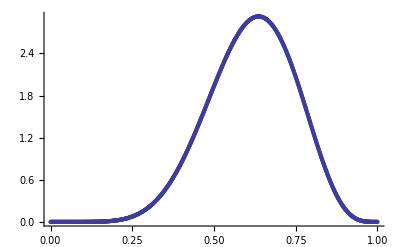

```mathematica
SetDirectory[NotebookDirectory[]]
fx = Import["OutFxn.dat"];
ListPlot[fx]
```

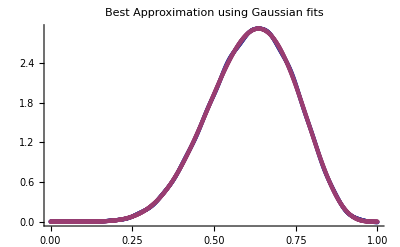

```mathematica
gepochs =Import@Last[Sort[FileNames[".\\Gauss\\*.dat"], (AbsoluteTime@FileDate@#1<AbsoluteTime@FileDate@#2)& ]];
Dimensions[gepochs];
ListPlot[{gepochs, fx}, PlotLabel-> "Best Approximation using Gaussian fits"]
```

```mathematica
triepochs =Import@Last[Sort[FileNames[".\\Tri\\*.dat"], (AbsoluteTime@FileDate@#1<AbsoluteTime@FileDate@#2)& ]];
Dimensions[triepochs];
ListPlot[{triepochs,fx}, PlotLabel-> "Best Approximation using Triangle fits"]
```

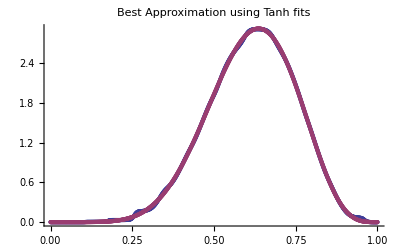

```mathematica
tanhepochs =Import@Last[Sort[FileNames[".\\Tanh\\*.dat"], (AbsoluteTime@FileDate@#1<AbsoluteTime@FileDate@#2)& ]];
Dimensions[tanhepochs];
ListPlot[{tanhepochs,fx}, PlotLabel-> "Best Approximation using Tanh fits"]
```

```mathematica
lpcepochs =Import@Last[Sort[FileNames[".\\Laplace\\*.dat"], (AbsoluteTime@FileDate@#1<AbsoluteTime@FileDate@#2)& ]];
Dimensions[lpcepochs]
ListPlot[{lpcepochs,fx}, PlotLabel-> "Best Approximation using Laplace fits"]
```

```mathematica
chyepochs =Import@Last[Sort[FileNames[".\\Cauchy\\*.dat"], (AbsoluteTime@FileDate@#1<AbsoluteTime@FileDate@#2)& ]];
Dimensions[chyepochs]
ListPlot[{chyepochs,fx}, PlotLabel-> "Best Approximation using Cauchy fits"]
```

```mathematica
sincepochs =Import@Last[Sort[FileNames[".\\Sinc\\*.dat"], (AbsoluteTime@FileDate@#1<AbsoluteTime@FileDate@#2)& ]];
Dimensions[sincepochs]
ListPlot[{sincepochs,fx}, PlotLabel-> "Best Approximation using Sinc fits"]
```

```mathematica
SetDirectory[$UserDocumentsDirectory];
```